```mathematica
Poljubno funkcijo f(x) se da razviti po Besselovih funkcijah Subscript[J, 0](Subscript[α, k0]/R x) na intervalu 0<x<R na sledeč način:
                f(x)=∑_(k=1)^∞ Subscript[C, k] Subscript[J, 0](Subscript[α, k0]/R x) ,     kjer je     Subscript[C, k]=1/(R^2/2 Subscript[J, 1]^2(Subscript[α, k0]))∫_0^R x f(x)Subscript[J, 0](Subscript[α, k0]/R x)ⅆx
```

```mathematica
(*Izračunaj prvih M členov  vrazvoju funkcije po Besselovi funkcijah na intervalu*)
f= (2+x)(20-11 x);
(*f= (2-x)(20-11 x);*)
M=4;
R=2;
ck =Table[

1/(R^2 /2 * BesselJ[1, BesselJZero[0,k]]^2)  NIntegrate[x f BesselJ[0,N[BesselJZero[0,k]] x/R], {x,0,R}]
, {k,1,M}] //N

(*za a rabimo še pripadajoče ortogonalne funkcije, da lahko naredimo pribljižek za iskano vsoto*)

gk = Table[

BesselJ[0, BesselJZero[0,k] x/R]
, {k,1,M}]
priblizek = Sum[ck[[n]] gk[[n]], {n,1,M}]

(*lažje*)
priblizek = ck.gk

(*Plot[{f,priblizek},{x,0,R}]*)

(*B točka, ker želimo sešteti vse elemente v seznamu*)

Sum[ck[[n]],{n,1,M}]
Total[ck]
```

```mathematica
(*Razvij funkcijo po legendrovih polinomih*)
f= Abs[x - 1/3];
M=4;
cn=Table[

Integrate[f* LegendreP[n,x],{x,-1,1}]/ Integrate[LegendreP[n,x]^2,{x,-1,1}]
,{n,0,M}
]
Pn= Table[LegendreP[n,x],{n,0,M}]


priblizek=cn.Pn


Sum[cn[[n]] Pn[[n]],{n,0,M}] (*Pazi indeksi grejo od prvega naprej! P0 je prvi element*)
Sum[cn[[n]] Pn[[n]],{n,1,M+1}] 

(*točka b vsota členov*)
Total[cn] //N

(*Če ne bi potrebovali vseh*)
Sum[cn[[n]],{n,1,M+1}] //N
```

```mathematica
(*Poišči ortogonalen polinom*)
p= x^3 + a x^2 +b x +c;
utez=x;
Solve[
{
Integrate[p*1*utez, {x,1,3}]==0,
Integrate[p*x*utez, {x,1,3}]==0,
Integrate[p*x^2*utez, {x,1,3}]==0
},{a,b,c}]//Flatten

p/.% /.x-> 3//N
```

```mathematica
M=13; (* ortogonalen polinom Če jih je preveč da bi ročno*)
a=1;
b=3;
utez= x;
x0=3;

p=x^M + Sum[c[n]x^n,{n,0,M-1}]
Table[ Integrate[p*x^n * utez,{x,a,b}],{n,0,M-1}];
Solve[%==0, Table[c[n],{n,0,M-1}]]

p/.%/.x-> x0 //N
```

```mathematica
M=5;
p= Sum[c[n]x^n,{n,0,M}]
utez=x;
Solve[

Table[Integrate[utez*x^n*p, {x,1,3}]==0,{n, 0, M-1}], (*Skupaj jih je 5!*)
Table[c[n],{n,0,M-1}]
] //Flatten
novp=p/. %

(*Še normiranost p: *)
Solve[Integrate[novp^2*utez,{x,1,3}]==1,c[M]]

(*Ne bomo dali flatten da vidimo da v obeh rešitvah dobimo enka rezulata*)
Abs[novp]/. % /. x-> 3 //N
```

```mathematica
Clear[x,y,u,v ]
DSolve[{u'[x]+y u[x] == y^2, u[0]==y+3}, u[x],x]
% /. {x-> 1, y-> 2}//N
```

```mathematica
(*Ločljive spremenljivke*)
Clear[x,y,u,c,U]
u=X[x]  Y[y]
D[u,x]/(x u)==- x D[u,y]/(x u)==k

DSolve[X'[x]/(x X[x])==k, X[x],x]//Flatten (*Rešitev za x*)
DSolve[-Y'[y]/Y[y]==k,Y[y],y]//Flatten (*Rešitev za y*)
U[x_,y_]=u/. %/.%%/. C[1]^2-> c
Solve[{U[1,1]==1,U[1,2]==2}, {c,k}, Reals]//Flatten

U[2,1]/.%//N
```

```mathematica
(*Poišči rešitev pe, vzemi prvih 5 členov*)

Clear[n,k,x,y,u,c,U,L,A,B]
(*Separacija*)
u=F[x] G[t]
D[u,x,x]/u==1/c^2 D[u,t,t]/u == -k^2(*homogeni robni pogoji*)



rF= DSolve[{F''[x]/F[x]==-k^2, F[0]==0}, F[x], x]/.C[2]-> 1// Flatten
Solve[(F[x]/.rF/. x-> L)==0,k]
k=n Pi/L




rG=DSolve[G''[t]/(c^2 G[t])==-k^2, G[t], t]/. {C[1]-> A[n], C[2]-> B[n]}//Flatten


(*Zaetni pogoji*)
U[x_,t_]=Sum[u/.rF/.rG,{n,1,Infinity}]
U[x,0]==x(L-x)
(*Dobili smo sinusno FV*)
A[n_]=2/L Integrate[x (L-x) Sin[n Pi x/L],{x,0,L}]

(*Drugi pogoj*)
(D[U[x,t],t]/. t-> 0)==0
B[n_]=0

(*Rešitev*)
c=1.5
L=3
U[x_,t_]=Sum[u/.rF/.rG,{n,1,5}](*Naaloga zahteva le 5!!! členov*)
U[1,2]//N
```

```mathematica
(*Dirichlet za notranjost kroga*)

Clear[A0,B0,A,B,a,b,u,r,φ ]
u[r_,φ_]=A0+B0 Log[r]+∑_(n=1)^∞ ( a[n] r^n+b[n] r^-n ) (A[n] Cos[n φ]+B[n] Sin[n φ]) /.{B0->0,b[n]-> 0,a[n]-> 1}

(*ker smo na krogu, lahko postavimo B0 in b na nič in celo a na 1*)
f=If[0< φ < π, π-Abs[π-2φ],0]
u[2,φ]==f(*Dobimo four vi+rsto na (-pi,pi). Pazi na koeficiente saj vsebujejo tudi 2^n*)


A0= 1/(2Pi)Integrate[f,{φ,-Pi,Pi}]
A[n_]=1/Pi Integrate[f Cos[n φ],{φ,-Pi,Pi}]/2^n
B[n_]=1/Pi Integrate[f Sin[n φ],{φ,-Pi,Pi}]/2^n
U[r_,φ_]= A0 +  Sum[r^n(A[n] Cos[n φ]+ B[n] Sin[n φ]), {n,1,5}]
u[1,2]//N
```

```mathematica
(*Neodvisna od kota/kotov, če smo v sferičnih -navadna De*)

Clear[u]
DSolve[{u''[r]+1/r u'[r]==0, u[1]==4, u[3]==8}, u[r],r]
%/. r->2//N
```

```mathematica
(*Metoda končnih razlik*)
a=1;A=4;b=3;B=-1;
n=12 ;h=(b-a)/n;
x[i_]:= a+ i h

(*Generiramo seznam enačb v vsaki notranji točki - torej naše približke vstavimo v DE*)resitev=Solve[Table[x[i]^2*(y[i+1]-2y[i]+y[i-1])/h^2+2 x[i]*(y[i+1]-y[i-1])/(2 h)-6 y[i]==x[i],{i,1,n-1} ]/.{y[0]-> A,y[n]-> B}, Table[y[i],{i,1,n-1}]]
215780464315/152741226249//N
y[2]/.resitev//N
```

```mathematica
(*Ekstremala funkcionala*)
f=y[x]^2*y'[x]^2;
Clear[x,y]
DSolveValue[{D[f,y[x]]-D[D[f,y'[x]],x]==0,y[1]==1,y[2]==2},y[x],x]
%/. x-> 3//N
```

```mathematica
(*Izoperimetrični problem*)
Clear[x,y]
f=y[x] x ^2+y'[x]^2 +  L x y[x];
Y= DSolveValue[{D[f,y[x]]-D[D[f,y'[x]],x]==0,y[1]==1,y[2]==2},y[x],x]
(*Lambdo pa določimo z integralskim pogojem*)
Solve[Integrate[x Y, {x,1,2}]==3,L]
Y/. % /. x-> 3 //N
```

```mathematica
f= y'[x]^2 +2 y[x] + LAM * 2y[x]
Y=DSolve[{D[f,y[x]]-D[D[f,y'[x]],x]==0, y[0]==0, y[1]==0.5}, y[x],x]
Solve[Integrate[1/2 (-LAM x+x^2+LAM x^2), {x,0,1}]==1/6,LAM] 
Y/.%/. x-> 1/3 //N
```

2 y[x]+2 LAM y[x]+y'[x]^2

{{y[x]→1/2 (-LAM x+x^2+LAM x^2)}}

{{LAM→0}}

{{{y[0.333333]→0.0555556}}}

```mathematica
Clear[x,y, Y, f, L]
f=2y[x] x +y'[x]^2 +  L x ^2y[x];
Y= DSolveValue[{D[f,y[x]]-D[D[f,y'[x]],x]==0,y[0]==1,y[1]==4},y[x],x]

Solve[Integrate[x^2 Y, {x,0,1}]==1,L]
Y/. % /. x-> 0.8 //N
```

1/24 (24+68 x-L x+4 x^3+L x^4)

{{L→140/9}}

{3.09896}

```mathematica
DSolve[{u''[r]+ 1/r u'[r]==0, u[1]==3, u[7]==8}, u[r], r]
%/. r-> 4 //N
```

{{u[r]→(3 Log[7]+5 Log[r])/Log[7]}}

{{u[4.]→6.56207}}

```mathematica
Clear[u, r]
DSolve[{u''[r]+1/r u'[r]==0, u[1]==3, u[7]==8}, u[r],r]
%/. r->4//N
```

{{u[r]→(3 Log[7]+5 Log[r])/Log[7]}}

{{u[4.]→6.56207}}

```mathematica
f= UnitStep[1/3] - UnitStep[-1/5]
Table[
LegendreP[n,x]

]
```

```mathematica
Clear[x,y]
f=4 x y[x]+y'[x]^2;
DSolveValue[{D[f,y[x]]-D[D[f,y'[x]],x]==0,y[0]==1,y[1]==0.3},y[x],x]
%/. x-> 0.6//N
```

0.333333 (3.-3.1 x+x^3)

0.452

UnitStep[-1+x]-UnitStep[-1/5+x]

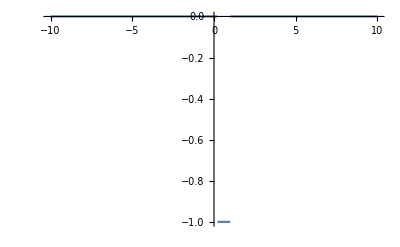

{-2/5,-18/25,-6/25,42/125,918/3125}

{1,x,1/2 (-1+3 x^2),1/2 (-3 x+5 x^3),1/8 (3-30 x^2+35 x^4)}

-2/5-(18 x)/25-3/25 (-1+3 x^2)+21/125 (-3 x+5 x^3)+(459 (3-30 x^2+35 x^4))/12500

-2/5+List^2-(18 x)/25-3/25 (-1+3 x^2)+21/125 (-3 x+5 x^3)

-2/5-(18 x)/25-3/25 (-1+3 x^2)+21/125 (-3 x+5 x^3)+(459 (3-30 x^2+35 x^4))/12500

-0.73024

-0.73024

-1.024

```mathematica
f=UnitStep[x-1] - UnitStep[x-1/5]
Plot[f,{x, -10,10}]
M=4;
cn=Table[

Integrate[f* LegendreP[n,x],{x,-1,1}]/ Integrate[LegendreP[n,x]^2,{x,-1,1}]
,{n,0,M}
]
Pn= Table[LegendreP[n,x],{n,0,M}]


priblizek=cn.Pn


Sum[cn[[n]] Pn[[n]],{n,0,M}] 
Sum[cn[[n]] Pn[[n]],{n,1,M+1}] 

Total[cn] //N
(*Če ne bi potrebovali vseh*)
Sum[cn[[n]],{n,1,M+1}] //N
Sum[cn[[n]],{n,1,M}] //N
```